# 1+1 QCD with Adjoint Fermions -- Classical Limit

```mathematica
(*This code reproduces the scattering of a classical Hamiltonian describing Num identical massless particles which have a preferred ordering with respect to their immediate neighbors. It arrises as the limit of QCD in 1+1 dimensions with adjoint fermions. Since the equations of motions of motion are piecewise constant, the dynamics are piecewise linear. The code below pastes together solutions, solving the matching conditions over the rationals given rational inital conditions. As a result, the dynamics are solved for exactly. Questions, bugs, comments, etc can be sent to jcd484@nyu.edu*)
```

```mathematica
Num=5;
(*Be careful with Num>7, it will be slow*)
```

## Definitions

```mathematica
newrandom:=Do[a0=Sort[RandomReal[{-15,15},Num]];p0=RandomReal[{-20,20},Num];p0=Reverse[Sort[p0]];p0=Rationalize[p0,.1];a0=Rationalize[a0,.1];,1];
(*newrandom will give random rationalized inital conditions when called*)
a=Table[Subscript[x, i][t],{i,1,Num,1}];
p=Table[Subscript[v, i][t],{i,1,Num,1}];
(*We then define our confining potential*)
V[σ_]:= (First[σ]-Last[σ])+Sum[RealAbs[σ[[i]]-σ[[i+1]]],{i,1,Length[σ]-1}];
Vp[a_]:=PiecewiseExpand[V[a]];
ExRelEqs[a_,p_]:=Join[MapThread[D[#1,t]==-#2&,{p,D[Vp[a],{a}]}],MapThread[D[#1,t]== If[#2>0,1,-1]&,{a,p}]];
(*The EOM are always piecewise constant, so here we expand them*)
exacts=PiecewiseExpand[ExRelEqs[a,p]];
(*We then solve and recombine, with the nontrivial information given by the piecewise conditions*)
exsols=DSolve[#,Flatten[{a,p}],t]&/@Internal`FromPiecewise[exacts][[2]];
functions=Table[PiecewiseExpand[Internal`ToPiecewise@@{Internal`FromPiecewise[exacts][[1]],Flatten[exsols[[All,All,i,2]]]}],{i,2*Num}];
functions=Flatten[Table[{functions[[i]],functions[[Num+i]]},{i,Num}]];
(*These functions give the dynamics of each particle given a spatial ordering and momemtun signs*)
```

```mathematica
(*Evolve just does the work of choosing and gluing the different solutions found above together to give the full scattering*)
```

```mathematica
Evolve[a0_,p0_]:=Module[{},newinits=Flatten[Table[{p0[[i]],a0[[i]]},{i,Num}]];
(*Initializing variables*)
whereamigoin={a0,p0};
tinit=0;
possols={};
momsols={};
steps={};
s=0;
While[True(*Loop should break itself later*),
(*Choose the dynamics given a particle ordering*)
thisround=Simplify[functions,Join[MapThread[#1== #2&,{a,whereamigoin[[1]]}],MapThread[#1== #2&,{p,whereamigoin[[2]]}]]];
(*Match free coefficients to initial conditions*)
toinit=thisround/.t->tinit;
rationals=FullSimplify[Flatten[MapThread[Solve[#1==#2,#3,Rationals]&,{toinit,newinits,Flatten[Table[{C[i],C[i+Num]},{i,Num}]]}]]];
evolve=thisround/.rationals;
posevol=Table[evolve[[2i]],{i,Num}];
momevol=Table[evolve[[2i-1]],{i,Num}];
possols=Join[possols,{posevol}];
momsols=Join[momsols,{momevol}];
(*Find the point where the next pair of particles cross, changing the ordering and thus the dynamics*)
intersect=Quiet[Table[If[i≠j,t/.Solve[{posevol[[i]]== posevol[[j]],tinit<t},t,Rationals],{-∞}],{j,Num},{i,Num}]];
(*Or when a particle should turn around*)
intersect2=Quiet[Table[t/.Solve[{momevol[[i]]== 0,tinit<t},t,Rationals],{i,Num}]];
intersect3=Join[{Flatten[intersect],Flatten[intersect2]}];
intersect4=Flatten[intersect3/.t->{-∞}];
(*Break the loop if there are no such points, and tell the solution this extends for all time*)
If[AllTrue[Flatten[intersect4],#== -∞&],steps=Join[steps,{t>tinit}]];
If[AllTrue[Flatten[intersect4],#== -∞&],Break[]];
forward=Select[intersect4-tinit,NonNegative];
(*Choose the most immediate event*)
tinter=Min[forward];
tinter=tinit+tinter;
newinits=evolve/.t->tinter;
(*Push the solution forward an epsilon amount just so the Piecewise has no trouble choosing which sector it's in*)
whereamigoin={posevol,momevol}/.t->tinter+20000*3*10^-16;
steps=Join[steps,{tinit<t<tinter}];
tinit=FullSimplify[tinter];]];
```

## Example

```mathematica
newrandom
a0
p0
(*Make sure that none of p0 come out as 0, rerun newrandom if so*)
```

{1/2,5/2,11/2,26/3,32/3}

{21/2,6/5,-14/3,-8,-9}

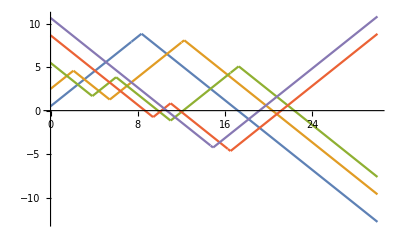

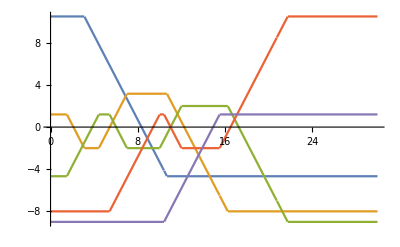

```mathematica
Evolve[a0,p0];
time=30;
posfull =Table[PiecewiseExpand[Internal`ToPiecewise@@{steps,possols[[All,i]]}],{i,Num}];
momfull =Table[PiecewiseExpand[Internal`ToPiecewise@@{steps,momsols[[All,i]]}],{i,Num}];
posplot=Plot[posfull,{t,0,time},PlotRange->Full(*,GridLines->{{Time[[l,1]],Time[[l,2]]}, {1,1}}*)]
momplot=Plot[momfull,{t,0,time}]
```

```mathematica
(*Check for momentum and energy conservation*)
```

```mathematica
initial=momfull/.t->$MachineEpsilon
final=momfull/.t->100
Total[initial]==Total[final]
Total[Abs[#]&/@final]==Total[Abs[#]&/@initial]
NumberForm[Total[Abs[#]&/@final],30]
NumberForm[Total[Abs[#]&/@initial],30]
```

{21/2,6/5,-14/3,-8,-9}

{-14/3,-8,-9,21/2,6/5}

True

True

1001/30

1001/30

## On a Circle

```mathematica
(*More or less the same as above. Set the radius of the circle by "r". One can create mesons by sending r->0, but make sure to change how comprandom sprinkles particles on the line.*)
```

```mathematica
r=1;
comprandom:=Do[a0=Sort[RandomReal[{0,r},Num]];p0=RandomReal[{-5,5},Num-1];p0=Reverse[Sort[p0]];p0=Rationalize[p0,.001];p0=Append[p0,-Total[p0]];a0=Rationalize[a0,.001];,1];
a=Table[Subscript[x, i][t],{i,1,Num,1}];
p=Table[Subscript[v, i][t],{i,1,Num,1}];
Vcomp[σ_]:= RealAbs[Last[σ]-First[σ]-r]+Sum[RealAbs[σ[[i]]-σ[[i+1]]],{i,1,Length[σ]-1}];
Vpcomp[a_]:=PiecewiseExpand[Vcomp[a]];
CompExRelEqs[a_,p_]:=Join[MapThread[D[#1,t]==-#2&,{p,D[Vpcomp[a],{a}]}],MapThread[D[#1,t]== If[#2>0,1,-1]&,{a,p}]];
compexacts=PiecewiseExpand[CompExRelEqs[a,p]];
compexsols=DSolve[#,Flatten[{a,p}],t]&/@Internal`FromPiecewise[compexacts][[2]];
compfunctions=Table[PiecewiseExpand[Internal`ToPiecewise@@{Internal`FromPiecewise[compexacts][[1]],Flatten[compexsols[[All,All,i,2]]]}],{i,2*Num}];
compfunctions=Flatten[Table[{compfunctions[[i]],compfunctions[[Num+i]]},{i,Num}]];
```

```mathematica
CompEvolve[a0_,p0_]:=Module[{},newinits=Flatten[Table[{p0[[i]],a0[[i]]},{i,Num}]];
whereamigoin={a0,p0};
tinit=0;
possols={};
momsols={};
steps={};
s=0;
While[tinit<25,
thisround=Simplify[compfunctions,Join[MapThread[#1== #2&,{a,whereamigoin[[1]]}],MapThread[#1== #2&,{p,whereamigoin[[2]]}]]];
toinit=thisround/.t->tinit;
rationals=FullSimplify[Flatten[MapThread[Solve[#1==#2,#3,Rationals]&,{toinit,newinits,Flatten[Table[{C[i],C[i+Num]},{i,Num}]]}]]];
evolve=thisround/.rationals;
posevol=Table[evolve[[2i]],{i,Num}];
momevol=Table[evolve[[2i-1]],{i,Num}];
possols=Join[possols,{posevol}];
momsols=Join[momsols,{momevol}];
intersect=Quiet[Table[If[i≠j&&i<j,t/.Solve[{posevol[[i]]== posevol[[j]],tinit<t},t,Rationals],{-∞}],{j,Num},{i,Num}]];
intersect2=Quiet[Table[t/.Solve[{momevol[[i]]== 0,tinit<t},t,Rationals],{i,Num}]];
(*Now also solves for when the first at last particle cross on the other side of the circle.*)
intersect5=Quiet[{t/.Solve[{Last[posevol]-First[posevol]== r,tinit<t},t,Rationals]}];
intersect3=Join[{Flatten[intersect],Flatten[intersect2],Flatten[intersect5]}];
intersect4=Flatten[intersect3/.t->{-∞}];
If[AllTrue[Flatten[intersect4],#== -∞&],steps=Join[steps,{t>tinit}]];
If[AllTrue[Flatten[intersect4],#== -∞&],Break[]];
forward=Select[intersect4-tinit,NonNegative];
tinter=Min[forward];
tinter=tinit+tinter;
newinits=evolve/.t->tinter;
whereamigoin={posevol,momevol}/.t->tinter+20000*3*10^-16;
steps=Join[steps,{tinit<t<tinter}];
tinit=FullSimplify[tinter];]];
```

```mathematica
(*Here we plot an example on the whole real line. You can mod out by r to visualize on the circle.*)
```

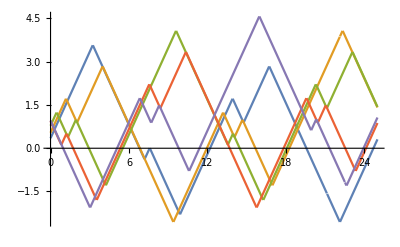

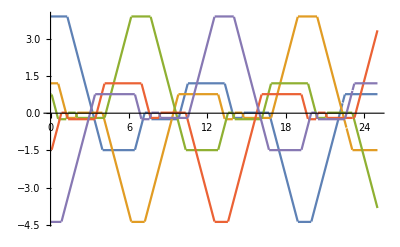

```mathematica
a0={8/23,7/13,25/32,16/17,25/26};
p0={152/39,59/49,23/30,-64/43,-3599023/821730};
CompEvolve[a0,p0];
time=25;
posfull =Table[PiecewiseExpand[Internal`ToPiecewise@@{steps,possols[[All,i]]}],{i,Num}];
momfull =Table[PiecewiseExpand[Internal`ToPiecewise@@{steps,momsols[[All,i]]}],{i,Num}];
posplot=Plot[posfull,{t,0,time},PlotRange->Full]
momplot=Plot[momfull,{t,0,time}]
```

```mathematica
(*Make sure to choose a time to compare such that the there is no force on any set of particles. Otherwise some energy will be lost to the string and below will not say "True" when comparing the kinetic energies.*)
```

```mathematica
initial=momfull/.t->$MachineEpsilon
final=momfull/.t->19
Total[initial]
Total[final]
N[Total[Abs[#]&/@final]]== N[Total[Abs[#]&/@initial]]
NumberForm[Total[Abs[#]&/@final],10]
NumberForm[Total[Abs[#]&/@initial],10]
```

{152/39,59/49,23/30,-64/43,-3599023/821730}

{-3599023/821730,152/39,59/49,23/30,-64/43}

0

0

True

112141/9555

112141/9555